SVG Exporter

BeginPackage["SVG`"];

⌈
	Simple SVG primitive support
⌋

ToSVG::usage=
	"Export to an SVG XMLObject"

BeginPackage["SVG`Package`"];

toXML::usage=
	"Turns svgElement structures into XML";

toEl::usage=
	"Turns aliases and standard SVG into svgElement data";

register::usage=
	"Registers a new transformable SVG element";
alias::usage=
	"Registers a new alias for toplevel elements in terms of SVG elements";

CSSGenerate::usage=
	"Copped from BTools. Just there to support style elements";

prepareSVGGraphics::usage="";
getViewBox::usage="";
getPlotRange::usage="";
axesAndFrame::usage="";
toSVGCore::usage="";
exportGraphics::usage="";
canonicalizeDirectives::usage="";
splitGraphicsList::usage="";

EndPackage[];

Begin["`Private`"];

⌈CSSGenerate⌋

⌈
	Used for styling things
⌋

⌈AllowedProperties⌋

$CSSDefaultAllowedProperties=
	Alternatives@@
		{
			"align-content","align-items","align-self",
			"all","animation","animation-delay",
			"animation-direction","animation-duration","animation-fill-mode",
			"animation-iteration-count","animation-name","animation-play-state",
			"animation-timing-function","backface-visibility","background",
			"background-attachment","background-blend-mode","background-clip",
			"background-color","background-image","background-origin",
			"background-position","background-repeat","background-size",
			"border","border-bottom","border-bottom-color",
			"border-bottom-left-radius","border-bottom-right-radius","border-bottom-style",
			"border-bottom-width","border-collapse","border-color",
			"border-image","border-image-outset","border-image-repeat",
			"border-image-slice","border-image-source","border-image-width",
			"border-left","border-left-color","border-left-style",
			"border-left-width","border-radius","border-right",
			"border-right-color","border-right-style","border-right-width",
			"border-spacing","border-style","border-top",
			"border-top-color","border-top-left-radius","border-top-right-radius",
			"border-top-style","border-top-width","border-width",
			"bottom","box-shadow","box-sizing",
			"caption-side","clear","clip",
			"color","column-count","column-fill",
			"column-gap","column-rule","column-rule-color",
			"column-rule-style","column-rule-width","column-span",
			"column-width","columns","content",
			"counter-increment","counter-reset","cursor",
			"direction","display","empty-cells",
			"filter","flex","flex-basis",
			"flex-direction","flex-flow","flex-grow",
			"flex-shrink","flex-wrap","float",
			"font","@font-face","font-family",
			"font-size","font-size-adjust","font-stretch",
			"font-style","font-variant","font-weight",
			"hanging-punctuation","height","justify-content",
			"@keyframes","left","letter-spacing",
			"line-height","list-style","list-style-image",
			"list-style-position","list-style-type","margin",
			"margin-bottom","margin-left","margin-right",
			"margin-top","max-height","max-width",
			"@media","min-height","min-width",
			"nav-down","nav-index","nav-left",
			"nav-right","nav-up","opacity",
			"order","outline","outline-color",
			"outline-offset","outline-style","outline-width",
			"overflow","overflow-x","overflow-y",
			"padding","padding-bottom","padding-left",
			"padding-right","padding-top","page-break-after",
			"page-break-before","page-break-inside","perspective",
			"perspective-origin","position","quotes",
			"resize","right","tab-size",
			"table-layout","text-align","text-align-last",
			"text-decoration","text-decoration-color","text-decoration-line",
			"text-decoration-style","text-indent","text-justify",
			"text-overflow","text-shadow","text-transform",
			"top","transform","transform-origin",
			"transform-style","transition","transition-delay",
			"transition-duration","transition-property","transition-timing-function",
			"unicode-bidi","user-select","vertical-align",
			"visibility","white-space","width",
			"word-break","word-spacing","word-wrap",
			"z-index","color","opacity",
			"background","background-attachment","background-blend-mode",
			"background-color","background-image","background-position",
			"background-repeat","background-clip","background-origin",
			"background-size","border","border-bottom",
			"border-bottom-color","border-bottom-left-radius","border-bottom-right-radius",
			"border-bottom-style","border-bottom-width","border-color",
			"border-image","border-image-outset","border-image-repeat",
			"border-image-slice","border-image-source","border-image-width",
			"border-left","border-left-color","border-left-style",
			"border-left-width","border-radius","border-right",
			"border-right-color","border-right-style","border-right-width",
			"border-style","border-top","border-top-color",
			"border-top-left-radius","border-top-right-radius","border-top-style",
			"border-top-width","border-width","box-shadow",
			"bottom","clear","clip",
			"display","float","height",
			"left","margin","margin-bottom",
			"margin-left","margin-right","margin-top",
			"max-height","max-width","min-height",
			"min-width","overflow","overflow-x",
			"overflow-y","padding","padding-bottom",
			"padding-left","padding-right","padding-top",
			"position","right","top",
			"visibility","width","vertical-align",
			"z-index","align-content","align-items",
			"align-self","flex","flex-basis",
			"flex-direction","flex-flow","flex-grow",
			"flex-shrink","flex-wrap","justify-content",
			"order","hanging-punctuation","letter-spacing",
			"line-height","tab-size","text-align",
			"text-align-last","text-indent","text-justify",
			"text-transform","white-space","word-break",
			"word-spacing","word-wrap","text-decoration",
			"text-decoration-color","text-decoration-line","text-decoration-style",
			"text-shadow","@font-face","font",
			"font-family","font-size","font-size-adjust",
			"font-stretch","font-style","font-variant",
			"font-weight","direction","unicode-bidi",
			"direction","user-select","border-collapse",
			"border-spacing","caption-side","empty-cells",
			"table-layout","counter-increment","counter-reset",
			"list-style","list-style-image","list-style-position",
			"list-style-type","@keyframes","animation",
			"animation-delay","animation-direction","animation-duration",
			"animation-fill-mode","animation-iteration-count","animation-name",
			"animation-play-state","animation-timing-function","backface-visibility",
			"perspective","perspective-origin","transform",
			"transform-origin","transform-style","transition",
			"transition-property","transition-duration","transition-timing-function",
			"transition-delay","box-sizing","content",
			"cursor","nav-down","nav-index",
			"nav-left","nav-right","nav-up",
			"outline","outline-color","outline-offset",
			"outline-style","outline-width","resize",
			"text-overflow","column-count","column-fill",
			"column-gap","column-rule","column-rule-color",
			"column-rule-style","column-rule-width","column-span",
			"column-width","columns","page-break-after",
			"page-break-before","page-break-inside","quotes",
			"filter"
			};

⌈AllowedTypes⌋

$CSSDefaultAllowedTypes=
	Alternatives@@
		{
			"a","abbr","acronym",
			"address","applet","area",
			"article","aside","audio",
			"b","base","basefont",
			"bdi","bdo","big",
			"blockquote","body",
			"br","button","buildto",
			"canvas","caption","center",
			"cite","code","col",
			"colgroup",
			"data","datalist",
			"dd","del","details",
			"dfn","dialog","dir",
			"div","dl","dt",
			"em","embed",
			"fieldset","figcaption","figure",
			"font","footer","form",
			"frame","frameset",
			"header","hr",
			"h1","h2","h3",
			"h4","h5","h6",
			"i","iframe","img",
			"inputcell",
			"input","ins",
			"kbd","keygen",
			"label","legend","li",
			"link",
			"main","map","mark",
			"menu","menuitem",
			"meta","meter",
			"nav","noframes",
			"noscript",
			"object","ol",
			"optgroup","option",
			"output",
			"p","param",
			"picture","pre",
			"progress",
			"q",
			"rp","rt","ruby",
			"s","samp","script",
			"section","select","small",
			"source","span","strike",
			"strong","style","sub",
			"summary","sup",
			"table","tbody","td",
			"textarea","tfoot","th",
			"thead","time","title",
			"tr","track","tt",
			"u","ul",
			"var","video",
			"wbr"
			};

⌈$CSSPropertyRules⌋

$CSSDefaultPropertyRules=
	{
		FontColor→"color",
		FrameStyle→"border",
		FrameMargins→"margin",
		TextAlignment→"text-align",
		TabSpacings→"tab-size",
		SourceLink→"src",
		ButtonFunction->
			"onclick",
		Annotation→"alt",
		Hyperlink→"href",
		RoundingRadius→"border-radius",
		LineSpacing→"line-height",
		ImageSize→{"width","height"},
		CellSize→{"width", "height"},
		e_:>
			(
				ToLowerCase[
					StringJoin@{
						StringTake[#,1],
						StringReplace[StringDrop[#,1],
							l:LetterCharacter?(Not@*LowerCaseQ):>"-"<>l]
						}&@ToString[e]
					]
				)
		};

⌈$CSSValueRules⌋

$CSSDefaultValueRules=
	Join[
		Map[
			Replace[#,
				Hold[c_]:>
					(c→ToLowerCase@ToString[Unevaluated[c]])
				]&,
			Thread@Hold@{
				Red,White,Blue,Black,Yellow,
				Green,Orange,Purple,Pink,Gray,
				LightBlue,LightRed,LightGray,LightYellow,
				LightGreen,LightOrange,LightPurple,LightPink,
				Thick,Dotted,Thin,Dashed
				}],{
		c_?ColorQ:>
			"#"<>Map[
				StringPadLeft[
					IntegerString[#,16],
					2,
					"0"
					]&,
				Floor[255*Apply[List,ColorConvert[c,RGBColor]]]
				],
		i_Integer:>
			ToString[i]<>"px",
		q_Quantity:>
			StringReplace[
				ToString[q],
				" "→""
				],
		Scaled[i_]:>
			ToString@Floor[i*100]<>"%",
		r_Rule:>
			(cssGenerate[r]),
		{l__}|Directive[l__]:>
			StringRiffle@Map[#/.$CSSValueRules&,{l}],
		d_Dynamic:>
			(Setting[d]/.$CSSValueRules),
		i_:>ToLowerCase@ToString[i]
		}
	];

⌈$CSSTypeRules⌋

$CSSDefaultTypeRules=
	{
		"Title"→"h1",
		"Subtitle"→"h2",
		"Section"→"h3",
		"Subsection"→"h4",
		"Subsubsection"→"h5",
		"Subsubsubsection"→"h6",
		"Hyperlink"→"a",
		"HyperlinkActive"→"a:hover",
		"Graphics"→"img",
		"Text"→"p",
		s_String:>(ToLowerCase[s])
		};

⌈cssThreadedOptions⌋

cssThreadedOptions[propBase_,propOps_,vals_]:=
	MapThread[
		If[!MatchQ[#2,Inherited|None],
			If[StringContainsQ[propBase,"-"],
				StringReplace[propBase,{
					"-"→("-"<>#<>"-")
					}]→(#2/.$CSSValueRules),
				StringJoin[propBase,"-"<>#]→(#2/.$CSSValueRules)
				],
			Nothing
			]&,{
		propOps,
		vals
		}]

⌈cssGenerate⌋

cssGenerate//Clear;
cssGenerate[
	prop_→val:Except[{__Rule}]
	]:=
	With[{
		propBase=
			prop/.$CSSPropertyRules
		},
		If[!MatchQ[propBase, $CSSAllowedProperties],
			Nothing,
			If[Not@ListQ@propBase,
				Sequence@@
						Replace[val,
							{
								{{l_,r_},{b_,h_}}:>
									If[StringContainsQ[propBase,"radius"],
										cssThreadedOptions[
											propBase,
											{"left-bottom","right-bottom","left-top","right-top"},
											{l,r,b,h}
											],
										cssThreadedOptions[
											propBase,
											{"left","right","bottom","top"},
											{l,r,b,h}
											]
										],
								{l_,r_}:>
									cssThreadedOptions[
										propBase,
										{"left","right"},
										{l,r}
										],
								v_:>
									{propBase→(v/.$CSSValueRules)}
								}
							],
				If[ListQ@val,
					Sequence@@cssGenerate[Thread[propBase→val]],
					cssGenerate[First@propBase→val]
					]
				]
			]
		];
cssGenerate[
	type:_String|_Symbol->spec:{__Rule}
	]:=
	With[{tp=ToString[type]/.$CSSTypeRules},
		If[!MatchQ[tp, $CSSAllowedProperties],
			Nothing,
			tp→Map[cssGenerate, spec]
			]
		];
cssGenerate[r:{__Rule}]:=
	cssGenerate/@r;
cssGenerate[a_Association]:=
	KeyValueMap[cssGenerate,a];
cssGenerate[{},Optional[_,_]]:={};

⌈generateCSSString⌋

generateCSSString[{}, _]:=""

generateCSSString[r:{__Rule}, riffle:_String:" "]:=
	StringRiffle[
		KeyValueMap[#<>": "<>#2<>";"&, Association[r]],
		riffle
		];
generateCSSString[r:{__Rule}, {riffle_String, _}]:=
	generateCSSString[r, riffle]

generateCSSString[a_Association?AssociationQ, 
	riffle:{_String, _String}:{" ", "
"}]:=
	StringRiffle[
		KeyValueMap[
				(#/.$CSSTypeRules)<>"{"<>riffle[[1]]<>
					generateCSSString[#2, riffle[[1]]]<>riffle[[1]]<>"}"&,
			a
			],
		riffle[[2]]
		];

⌈generateObjectStyles⌋

generateObjectStyles//Clear

generateObjectStyles[nb_NotebookObject]:=
	Prepend[
		AssociationMap[
			AbsoluteCurrentValue[nb, {StyleDefinitions, #}]&,
			Select[StringQ]@Keys@
				FE`Evaluate@
					FEPrivate`GetPopupList[nb,"MenuListStyles"]
			],
		"body"→Options[nb]
		]

generateObjectStyles[cell_CellObject]:=
	Normal@Merge[
		{
			Options[cell],
			AbsoluteCurrentValue[ParentNotebook[cell],
				{StyleDefinitions, NotebookRead[cell][[2]]}
				]
			},
		First
		]

generateObjectStyles[box_BoxObject]:=
	Options[box];

⌈CSSGenerate⌋

Options[CSSGenerate]=
	{
		"PropertyMapping"→Automatic,
		"AllowedProperties"→Automatic,
		"ValueMapping"→Automatic,
		"TypeMapping"→Automatic,
		"AllowedTypes"→Automatic,
		"GenerateString"→True,
		"RiffleCharacter"→{" ", "
"}
		};
CSSGenerate[l:(_List?OptionQ|_Association?(OptionQ@*Normal)), ops:OptionsPattern[]]:=
	Block[
		{
			$CSSPropertyRules=
				Replace[OptionValue["PropertyMapping"],
					Except[_?OptionQ]:>$CSSDefaultPropertyRules
					],
			$CSSValueRules=
				Replace[OptionValue["ValueMapping"],
					Except[_?OptionQ]:>$CSSDefaultValueRules
					],
			$CSSTypeRules=
				Replace[OptionValue["TypeMapping"],
					Except[_?OptionQ]:>$CSSDefaultTypeRules
					],
			$CSSAllowedProperties=
				Replace[OptionValue["AllowedProperties"],
					{
						{s__String}:>
							Alternatives[s],
						Except[_Alternatives]:>
							$CSSDefaultAllowedProperties
						}
					],
			$CSSAllowedTypes=
				Replace[OptionValue["AllowedTypes"],
					{
						{s__String}:>
							Alternatives[s],
						Except[_Alternatives]:>
							$CSSDefaultAllowedTypes
						}
					]
			},
		If[TrueQ@OptionValue["GenerateString"], 
			generateCSSString[#, 
				Replace[OptionValue["RiffleCharacter"], 
					{
						s_String?StringQ:>
							{s, "
"},
						Except[{_String?StringQ, _String?StringQ}]:>
							{" ", "
"}
						}]
				]&,
			Identity
		 ]@
			If[AllTrue[Values@l, OptionQ],
				Map[cssGenerate, 
					If[$CSSAllowedTypes===All,
						Association[l],
						KeySortBy[FirstPosition[$CSSTypeRules, #/.$CSSTypeRules]&]@
							KeySelect[Association[l], 
								MatchQ[#/.$CSSTypeRules, $CSSAllowedTypes]&
								]
						]
					],
				cssGenerate[l]
				]
		]

CSSGenerate[
	nb:
		_NotebookObject|_CellObject|_BoxObject|
		_FrontEnd`EvaluationNotebook|_FrontEnd`InputNotebook:FrontEnd`InputNotebook[], 
	ops:OptionsPattern[]
	]:=
	CSSGenerate[generateObjectStyles[FE`Evaluate@nb], ops]

⌈toXML⌋

⌈toNotStupidString⌋

⌈
	ToString[x*10^7] is ridiculously stupid so we need to do this to fix it
⌋

toNotStupidString[n_?IntegerQ]:=
	StringTrim[Quiet@ToString@NumberForm[n, ExponentFunction->(Null&)], "."];
toNotStupidString[n_?NumericQ]:=
	StringTrim[Quiet@ToString@NumberForm[N@n, ExponentFunction->(Null&)], "."];
toNotStupidString[e_]:=
	ToString@e

⌈$SVGColorMap⌋

$SVGColorMap=
	KeyMap[
		ReleaseHold,
		AssociationMap[
			Replace[Hold[a_]:>ToLowerCase@SymbolName[Unevaluated[a]]],
			Thread@Hold@{
				Black, White, Gray,
				Red, Blue, Green, Yellow,
				Orange, Pink, Purple
				}
			]
		]

⌈$SVGValMap⌋

$SVGValMap=
	Join[
		$SVGColorMap,
		KeyMap[N, $SVGColorMap],
		<|
			(* other directly convertable values *)
			None→"none",
			Opacity[0]→"none",
			Opacity[0.]→"none",
			Automatic→"auto"
			|>
		]

⌈ScalingFactors⌋

$symbScalingFactors=
	6*10^-2*<|
		Tiny→.005,
		Small→.01,
		Medium→.05,
		Large→.1
		|>

$symbDashingFactors=
	Map[#*{2, .6}&]@<|
		Tiny→.005,
		Small→.01,
		Medium→.05,
		Large→.1
		|>

⌈toSVGString⌋

⌈
	This attempts to take an SVG option value and get a proper string representation for it. There is some hacky-ness as handling of things like Dashing[{Small, Small}] must be different from that of Thickness[Large]. Hopefully this can be cleaned sometime.
⌋

toSVGString//Clear

toSVGString[Scaled[s_], __]:=
	toNotStupidString[Floor@100*s]<>"%";
toSVGString[RGBColor[r__], h__]:=
	"#"<>IntegerString[Floor[{r}*255], 16, 2];
toSVGString[h_?ColorQ, __]:=
	toSVGString[ColorConvert[h, RGBColor], None, None];
toSVGString[v_, _, "Style"]:=
	CSSGenerate[Flatten@{Normal@v}];
toSVGString[v_, _, "Thickness"]:=
	toSVGString[Scaled[v], None, None];
toSVGString[v_, _, "AbsoluteThickness"]:=
	toSVGString[If[NumericQ@v, Max@{v, 1}, v], None, None]<>"pt";
toSVGString[l_List, _, "Dashing"]:=
	StringRiffle@Map[ToString]@
		Module[
			{
				vbmin=$svgViewBox[[3]](*Min[$svgViewBox[[3;;]]]*)
				},
			MapIndexed[
				Replace[$symbDashingFactors[#],
					{
						m_Missing:>#,
						e_:>e[[Mod[#2[[1]], 2, 1]]]*vbmin
						}
					]&,
				l
				]
			];
toSVGString[(h:Except[List])[x_], _, _]:=(* handling things like Rotate *)
	ToLowerCase@ToString[h]<>"("<>toSVGString[x, None, None]<>")";
toSVGString[a_, head_, _]:=
	Block[
		{
			$scaling=$symbScalingFactors
				(*If[head==="stroke-dasharray", $symbDashingFactors, $symbScalingFactors]*),
			vbmin=$svgViewBox[[3]](*Min[$svgViewBox[[3;;]]]*)
			},
		a//.{(* a bunch of junk to handle symbolic sizes *)
				k:Alternatives@@Keys[$scaling]:>
					Lookup[$scaling, k]*vbmin
				}//ReplaceAll@{
				{n_?NumericQ, m_?NumericQ}:>
					(
						toNotStupidString[n]<>","<>toNotStupidString[m]
						),
				e:_?NumericQ:>toNotStupidString[e]
				}//
			Replace@{
				l_List:>StringRiffle[ToString/@l],
				e_:>ToString@e
				}
		]

⌈$SVGPropMap⌋

$SVGFacePropMap=
	KeyMap[SymbolName]@<|
		Filling→"fill",
		Opacity→"fill-opacity",
		RoundingRadius→{"rx", "ry"}
		|>;
$SVGEdgePropMap=
	KeyMap[SymbolName]@<|
		LineColor→"stroke",
		Filling→"stroke",
		RoundingRadius→"stroke-round",
		CapForm→"stroke-linecap",
		Thickness→"stroke-width",
		AbsoluteThickness->"stroke-width",
		JoinForm→"stroke-linejoin",
		Dashing→"stroke-dasharray",
		AbsoluteDashing→"stroke-dasharray"
		|>;

$SVGPropMap=
	KeyMap[SymbolName]@<|
		TransformationFunction→"transform",
		FontFamily→"font",
		Style→"style"
		|>

⌈toSVGProp⌋

⌈
	Builds an attribute rule for an SVG elements. This has to handle face and edge elements differently so there are different prop maps for each.
⌋

toSVGProp//Clear

(*decamel[s_]:=
	StringTrim[
		StringJoin@
			StringSplit[s, l:LetterCharacter?(Not@*LowerCaseQ):>"-"<>ToLowerCase@l],
		Except[LetterCharacter]
		]*)

toSVGProp[(form:EdgeForm|FaceForm|None)[key_], val_]:=
	Module[{k1, k, m},
		k1=k=ToString@key;
		m=
			Which[
				form===EdgeForm, 
					$SVGEdgePropMap, 
				form===FaceForm,
					$SVGFacePropMap,
				True,
					$SVGPropMap
				];
		k=Lookup[m, k, Lookup[$SVGPropMap, k, If[StringQ@key, k(*decamel[k]*), None]]];
		Which[
			k===None,
				Nothing,
			ListQ@k,
				MapThread[
					#->Lookup[$SVGValMap, Key@#2, toSVGString[#2, #, k1]]&,
					{
						k,
						val
						}
					],
			True,
				k->Lookup[$SVGValMap, Key@val, toSVGString[val, k, k1]]
			]
		];
toSVGProp[key_, val_]:=
	toSVGProp[None@key, val]

⌈toXML⌋

toXML//Clear

toXML[svgElement[head_, attrs_]]:=
	XMLElement[head, 
		DeleteDuplicatesBy[First]@KeyValueMap[toSVGProp,
			KeyDrop[Association@attrs, "Body"]
			],
		Flatten@List@ReplaceAll[
			Lookup[attrs, "Body", {}],
			s:(Alternatives@@Map[Blank, Prepend[Keys@$svgPrimitives, svgElement]]):>
				toXML@toEl[s]
			]
		]

⌈toEl⌋

⌈
	This defines the DSL and primary aliasing for Mathematica objects. Extra rules can be added in the Aliases section.
⌋

ClearAll@toEl

toEl~SetAttributes~Listable

opsPatRule=(_FaceForm|_EdgeForm|_String|_Symbol)→_;
opsPat[]=___?(MatchQ[Flatten[{#}], {opsPatRule...}]&);
notOp[]:=_?(Not@MatchQ[Flatten@{#}, {opsPatRule...}]&)

$toElConvertsFully=True;

⌈register⌋

$svgPrimitives=
	<|
		
		|>;

register[fn_, head_, args__]:=
	With[{flargs=Flatten@{args}},
		$svgPrimitives[fn]=head;
		Replace[
			{
				{args}/.(pat_→key_String):>pat,
				Cases[flargs, (_→key_String):>key],
				Thread[
					Replace[flargs, 
						{
							(Verbatim[Pattern][a_, _]→key_String):>Hold[a],
							(
								(Optional|PatternTest|Condition)[Verbatim[Pattern][a_, _], _]→key_String
								):>Hold[a],
							_→Nothing
							}, 
						1
						], 
					Hold
					]
				},
			{
				{
					{pats__},
					vars_,
					Hold[vals_]
					}:>
				(
					toEl[svg:fn[pats, ops:opsPat[]]]:=
						If[TrueQ@$toElConvertsFully,
							svgElement[head, 
								Merge[
									{
										Thread[vars→vals],
										ops
										},
									First
									]
								],
							svg
							]
					),
				_:>Failure["RegistrationFailure",
					<|
						"MessageTemplate"->
							"Failed to register conversion rule for head `` and type `` with argspec ``",
						"MessageParameters":>
							{fn, head, {args}}
						|>
					]
				}
		]
	]

⌈alias⌋

ClearAll@alias;
ClearAll@aliasedQ;
ClearAll@aliasTarget;
ClearAll@lineTypeAlias;

alias/:(alias[lineType:True|False][expr_]:=form_):=
	Block[{$svgLineType=False},
		aliasedQ[expr]=True;
		lineTypeAlias[expr]=lineType;
		aliasTarget[expr]=
			FirstCase[
				HoldComplete[form],
				Alternatives@@Keys[$svgPrimitives],
				None,
				∞,
				Heads→True
				];
		toEl[expr]:=toEl[form]
		];
alias/:(alias[expr_]:=form_):=
	(alias[False][expr]:=form)

⌈Fallthrough⌋

toEl[e:_svgElement|_XMLElement|_Failure]:=
	e;

toEl[e_]:=
	Failure["XMLConversion", 
		<|
			"MessageTemplate"→"Failed to convert ``",
			"MessageParameters":>{e}
			|>
		]

⌈circle⌋

register[svgCircle, "circle", 
	{cx_?NumericQ→"cx", cy_?NumericQ→"cy"}, 
	r_?NumericQ→"r"
	]

⌈ellipse⌋

register[svgEllipse, "ellipse", 
	{cx_?NumericQ→"cx", cy_?NumericQ→"cy"}, 
	{rx_?NumericQ→"rx", ry_?NumericQ→"ry"}
	]

⌈line⌋

register[svgLine, "line", 
	{
		{x1_?NumericQ→"x1", y1_?NumericQ→"y1"}, 
		{x2_?NumericQ→"x2", y2_?NumericQ→"y2"}
		}
	]

⌈path⌋

register[svgPath, "path", path_?StringQ→"d"]

⌈polygon⌋

register[svgPolygon, "polygon", 
	pts:{
		{_?NumericQ, _?NumericQ}..
		}→"points"
	]

⌈polyline⌋

register[svgPolyline, "polyline", 
	pts:{
		{_?NumericQ, _?NumericQ}..
		}→"points"
	]

⌈rect⌋

register[svgRect, "rect", 
	{x_?NumericQ→"x", y_?NumericQ→"y"},
	{w_?NumericQ→"width", h_?NumericQ→"height"}
	]

⌈marker⌋

register[svgMarker, "marker", id_?StringQ→"id", body_→"Body"]

⌈text⌋

register[svgText, "text", body_→"Body", {x_?NumericQ→"x", y_?NumericQ→"y"}]

⌈title⌋

register[svgTitle, "title", body_→"Body"]

⌈group⌋

register[svgGroup, "g", (bodies:{__})→"Body"];

⌈Aliases⌋

⌈
	Need to handle some kind of directive stack that things get pushed onto when recursing.
Currently directives have to be manually passed down but this isn’t the eventual goal.
⌋

⌈adjustCoord⌋

⌈
	Little function to get the coordinate system corrected
⌋

adjustCoordC=
	Compile[{{xy, _Real, 1}, {pr, _Real, 2}, {scaling, _Real, 1}},
		{xy[[1]]*scaling[[1]], pr[[2, 2]]-(scaling[[2]]*xy[[2]]-pr[[2, 1]])},
		RuntimeOptions→"Speed",
		RuntimeAttributes→{Listable}
		];
adjustCoord[blah_]:=
	adjustCoordC[blah, $svgPlotRange, $svgScaling]

⌈Disk⌋

alias@
Disk[center_, rad:notOp[]:Automatic, ops:opsPat[]]:=
	If[ListQ@center[[1]],
		MapThread[svgCircle[##, ops]&, 
			{
				adjustCoord@center, 
				Replace[rad, {
					r_?NumericQ:>ConstantArray[r, Length@center],
					Except[{__?NumericQ}]:>
						ConstantArray[1., Length@center],
					e_:>
						PadRight[e, Length@center, e][[;;Length@center]]
					}]
				}
			],
		If[!NumericQ@rad,
			Ellipsoid[center, rad, ops],
			svgCircle[adjustCoord@center, 
				Replace[rad,
					Except[_?NumericQ]→1
					], 
				ops
				]
			]
		]

alias@
DiskBox[a___]:=
	Disk[a];

⌈Circle⌋

alias[True]@
Circle[center_, rad:notOp[]:Automatic, ops:opsPat[]]:=
	toEl[Disk[adjustCoord@center, rad, ops]]/.
		svgElement["circle", a_]:>svgElement["circle", Append[a, FaceForm[Filling]→None]]

alias@
CircleBox[a___]:=
	Circle[a]

⌈Ellipsoid⌋

alias@
Ellipsoid[center_, radii_, ops:opsPat[]]:=
	svgEllipsoid[adjustCoord@center, radii, ops]

⌈Rectangle⌋

alias@
Rectangle[{xmin_, ymin_}, {xmax_, ymax_}, ops:opsPat[]]:=
	svgRect[adjustCoord@{xmin, ymin}, {xmax-xmin, ymax-ymin}, ops]

alias@
Rectangle[{xmin_, ymin_}, ops:opsPat[]]:=
	svgRect[adjustCoord@{xmin, ymin}, Lookup[Flatten@{ops}, ImageSize, {1, 1}], ops]

alias@
RectangleBox[a___]:=
	Rectangle[a];

⌈Polygon⌋

alias@
Polygon[pts:{{_?NumericQ, _?NumericQ}..}, ops:opsPat[]]:=
	svgPolygon[adjustCoord@pts, ops]
alias@
Polygon[poly:{{{_?NumericQ, _?NumericQ}..}..}, ops:opsPat[]]:=
	svgPolygon[adjustCoord@#, ops]&/@poly

alias@
PolygonBox[a___]:=
	Polygon[a];

⌈Line⌋

alias[True]@
Line[pts:{{_?NumericQ, _?NumericQ}, {_?NumericQ, _?NumericQ}}, ops:opsPat[]]:=
	svgLine[adjustCoord@pts, ops]

alias[True]@
Line[pts:{{_?NumericQ, _?NumericQ}..}, ops:opsPat[]]:=
	With[{dat=adjustCoord@pts},
		svgPolyline[adjustCoord@pts, FaceForm[Filling]→None, ops]
		]

alias@
LineBox[a___]:=
	LineBox[a];

⌈Arrow⌋

arrowMarker//Clear

arrowMarker[ops:opsPat[]]:=
	Module[
		{
			heads=Lookup[ops, EdgeForm@Arrowheads, ops]
			},
		svgMarker["arrow-"<>StringTake[ToString@Hash@ops, 5],
			svgPath@"M0,0 L0,6 L9,3 z",
			"markerWidth"→10,
			"markerHeight"→10,
			"refX"→0,
			"refY"→0,
			"orient"→Automatic,
			"markerUnits"->"strokeWidth",
			ops
			]
		]

alias[True]@
Arrow[pts:{{_?NumericQ, _?NumericQ}..}, setBack:notOp[]:Automatic, ops:opsPat[]]:=
	(* I'm ignoring setBack for now but I'll have to handle it some day... *)
	With[{mark=arrowMarker[ops]},
		Sow@mark;
		Line[pts, ops, "marker"→URL[mark[[1]]]]
		]

alias@
ArrowBox[a___]:=
	Arrow[a];

⌈GraphicsComplex⌋

alias@
g:GraphicsComplex[pts_, data_, o___]:=
	toSVGCore[
		Flatten@Replace[Normal@g,
			gc_GraphicsComplex:>
				With[{map=AssociationThread[Range[Length@pts], pts]},
					data/.map (* this isn't actually going to be entirely clean, but it's good enough for now *)
					]
			],
		{o}
		]

alias@
GraphicsComplexBox[a___]:=
	GraphicsComplex[a];

⌈Text⌋

alias@
Text[body_, coord_, diffs:{_, _}|None:None, o:opsPat[]]:=
	With[
		{
			bops=If[MatchQ[body, Style], List@@Rest@body, {}],
			boo=toNotStupidString@If[MatchQ[body, Style], First@body, body]
			},
		svgText[
			boo, adjustCoord@coord, 
			Sequence@@If[diffs===None, 
				{},
				{
					Which[
						diffs[[1]]>=.5,
							"text-anchor"→"end",
						diffs[[1]]<=-.5,
							"text-anchor"→"start",
						True,
							"text-anchor"→"middle"
						],
					Which[
						diffs[[2]]>=.5,
							"dominant-baseline"→"hanging",
						diffs[[2]]<=-.5,
							"dominant-baseline"→"baseline",
						True,
							"dominant-baseline"→"middle"
						]
					}
				], 
			DeleteCases[
				Flatten@{
					o,
					Style->bops
					},
				EdgeForm[Thickness]→_
				]
			]
		]

⌈Tooltip⌋

alias@
Tooltip[body_, spec_, o:opsPat[]]:=
	svgGroup[
		{
			svgTitle[spec],
			toSVGCore[body, o]
			}
		]

⌈Dynamic⌋

alias@
Dynamic[body_, blah:notOp[]:Automatic, o:opsPat[]]:=
	body;

⌈TransparentObjects⌋

alias@
StatusArea[body_, spec_, o:opsPat[]]:=
	body;

⌈Rotate⌋

⌈
	This doesn’t actually work yet...
⌋

alias@
Rotate[g_, q_]:=
	Append[g, TransformationFunction→Rotate[q*Degree]]

⌈Annotation⌋

alias@
Annotation[a_, d_, ___]:=
	toSVGCore[a,
		{"AnnotationData"→d}
		];

⌈ToSVG⌋

⌈ToSVG⌋

⌈
	This is the main function. Currently I only allow Graphics to be passed in.
	It parse the directives into rules which are all wrapped in FaceForm or EdgeForm to specify to which they should apply.
	These then get fed to the DSL convert, then finally get pushed through to the XMLElement generator. The latter probably needs the most work.
⌋

ToSVG//Clear
ToSVG[g_Graphics, ops:OptionsPattern[]]:=
	Module[
		{
			imsize,
			viewbox,
			pr,
			scalingFactors,
			g2,
			svgBody,
			defs
			},
		{pr, viewbox, imsize, scalingFactors, g2}=
			prepareSVGGraphics[g, ops];
		Block[
			{
				$svgPlotRange=pr,
				$svgViewBox=viewbox,
				$svgViewSize=imsize,
				$svgScaling=scalingFactors
				},
			Quiet[
				svgBody=Reap[toXML/@Flatten@toSVGCore[First@g2, Flatten@{ops}]];
				defs=Flatten@svgBody[[2]],
				{
					(* optx messages don't matter here, so we quiet them if they show up *)
					GraphicsComplex::optx,
					GraphicsComplex::optrs
					}
				];
			XMLElement["svg",
				Flatten@{
					Thread[
						{"width","height"}->Map[toNotStupidString]@Floor@imsize
						],
					"viewbox"→StringRiffle@Map[toNotStupidString]@viewbox,
					(*"preserveAspectRatio"→"none",*)
					"version"→"1.1",
					{"http://www.w3.org/2000/xmlns/","xmlns"}→"http://www.w3.org/1999/xhtml"
					},
				If[Length@defs>0,
					Prepend@XMLElement["defs",
						{},
						toXML@*toEl/@DeleteDuplicates@defs
						],
					Identity
					]@
					svgBody[[1]]
				]
			]
		]

⌈prepareSVGGraphics⌋

prepareSVGGraphics[g_Graphics, ops:OptionsPattern[]]:=
	Module[
		{
			opp=Flatten@{ops, Options[g]},
			imsize,
			viewbox,
			pr,
			prpad,
			svgBody,
			defs,
			extra,
			$$,
			asp,
			scalingFactors,
			gpr
			},
		asp=Replace[OptionValue[Graphics, opp, AspectRatio], Except[_?NumericQ]→1];
		imsize=
			4/3*Replace[OptionValue[Graphics, opp, ImageSize],
				{
					Automatic:>
					 {1, asp}*360,
					n_?NumericQ:>
						{1, asp}*n
					}
				];
		gpr=getPlotRange@g;
		viewbox=Flatten@Transpose@gpr;
		prpad=
			Replace[OptionValue[Graphics, opp, PlotRangePadding],
				{
					i:_?NumericQ|_Scaled:>{i, i},
					Except[{_, _}]->{Scaled[.02], Scaled[.02]}
					}
				];
		{prpad, viewbox}=getViewBox[viewbox, prpad, imsize];
		extra=axesAndFrame[opp, gpr, prpad];
		scalingFactors=imsize/viewbox[[3;;4]];
		If[Length@extra>1,
			{$$, viewbox}=getViewBox[viewbox, {Scaled[.10], Scaled[0]}, imsize];
			];
		viewbox*=Join[scalingFactors, scalingFactors];
		gpr*=scalingFactors;
		imsize=Ceiling@viewbox[[3;;4]];
		{gpr, viewbox, imsize, scalingFactors, ReplacePart[g, 1->{extra, First@g}]}
		]

⌈getPlotRange⌋

igetPlotRange[g_]:=
	Module[
		{
			plop,
			cbs,
			xdim,
			ydim
			},
		plop=Lookup[Options[g, PlotRange], PlotRange, All];
		If[AllTrue[Flatten@plop, NumericQ],
			plop,
			cbs=CoordinateBounds@Cases[g[[1]], {_?NumericQ, _?NumericQ}, ∞];
			xdim=cbs[[1, 2]]-cbs[[1, 1]];
			ydim=cbs[[2, 2]]-cbs[[2, 1]];
			plop=Nest[
				Replace[
					{
						{a:{_, _}, b:Except[{_, _}]}:>{a, {b, b}},
						{b:Except[{_, _}], a:{_, _}}:>{{b, b}, a},
						{a:Except[{_, _}], b:Except[{_, _}]}:>{{a, a}, {b, b}},
						e:Except[{{_, _}, {_, _}}]:>{{e, e}, {e, e}}
						}
					], 
				plop, 
				3]/.(All|Automatic→Scaled[1]);
			{
				{
					Replace[plop[[1, 1]],
						Scaled[s_]:>cbs[[1, 2]]-xdim*s
						],
					Replace[plop[[1, 2]],
						Scaled[s_]:>cbs[[1, 1]]+xdim*s
						]
					},
				{
					Replace[plop[[2, 1]],
						Scaled[s_]:>cbs[[2, 2]]-ydim*s
						],
					Replace[plop[[2, 2]],
						Scaled[s_]:>cbs[[2, 1]]+ydim*s
						]
					}
				}
			]
		];

getPlotRange[g_Graphics]:=
	Quiet@Check[PlotRange@g, igetPlotRange@g]

⌈getViewBox⌋

⌈
	Handling things like the PlotRangePadding is non-trivial. 
	This is probably only like 50% of the way there.
⌋

getViewBox[view_, pad_, size_]:=
	Module[
		{
			viewbox=view,
			prpad=pad
			},
		viewbox=Join[viewbox[[;;2]], viewbox[[3;;]]-viewbox[[;;2]]];
		prpad=
			Replace[
				prpad,
				{
					{i:_?NumericQ|_Scaled, j:_?NumericQ|_Scaled}:>
						({{i/2, j/2}, {i/2, j/2}}/.(Scaled[a_]/2):>Scaled[a/2]),
					{l_List, e:Except[_List]}:>
						{l, {e, e}},
					{e:Except[_List], l_List}:>
						{{e, e}, l}
					}
				];
		prpad=
			prpad//.{
				{Scaled[x_], y_}:>
					{viewbox[[3]]*x, y},
				{x_, Scaled[y_]}:>
					{x, viewbox[[4]]*y}
				};
		{
			prpad,
			viewbox+Join[-prpad[[1, ;;2]], prpad[[1]]+prpad[[2]]]
			}
		]

⌈axesAndFrame⌋

getPlotTicksObjects[{{xmin_, xmax_}, {ymin_, ymax_}}, {x0_, y0_}]:=
	Module[{xbase, ybase, ends, xdiff, ydiff},
		xbase=Charting`ScaledTicks[{Identity,Identity}][xmin, xmax, 25];
		ybase=Rest@Charting`ScaledTicks[{Identity,Identity}][ymin, ymax, 25];
		{xbase, ybase}=
			MapIndexed[
				If[Mod[#2[[1]], 5]==4, 
					ReplacePart[#, 3→{2, 1}*#[[3]]],
					ReplacePart[#, 2→""]
					]&,
				#
				]&/@{xbase, ybase};
		xdiff=(xmax-xmin);
		ydiff=(ymax-ymin);
		{
			Function[
				ends={{#[[1]], y0-ydiff*#[[3, 2]]}, {#[[1]], y0+ydiff*#[[3, 1]]}};
				{
					If[#[[2]]=!="", 
						Text[ToString@#[[2]], ends[[1]], {0, 1.2}], 
						Nothing
						], 
					Line[ends]
					}
				]/@xbase,
			Function[
				ends={{x0-xdiff*#[[3, 2]], #[[1]]}, {x0+xdiff*#[[3, 1]], #[[1]]}};
				{
					If[#[[2]]=!="", Text[ToString@#[[2]], ends[[1]], {1.2, 0}], Nothing], 
					Line[ends]
					}
				]/@ybase
			}
		]

axesAndFrame[opp_, prange_, pad_]:=
	Module[
		{
			pr=prange+{{-1, 1}, {-1, 1}}*pad,
			axes,
			aticks,
			ast,
			orgy,
			axesLines,
			fst,
			frame,
			frameLines,
			axesTicks,
			frameTicks,
			tst
			},
		axes=
			Replace[OptionValue[Graphics, opp, Axes], 
				{
					Automatic→{False, False},
					e:Except[{_, _}]:>{e, e}
					}
				];
		orgy=
			Replace[OptionValue[Graphics, opp, AxesOrigin], 
				{
					e:Except[{_, _}]:>{prange[[1, 1]], prange[[2, 1]]}
					}
				];
		ast=Replace[OptionValue[Graphics, opp, AxesStyle],
			{
				{}|Automatic:>{Automatic, Automatic},
				e:Except[{_, _}]:>{e, e}
				}
			]/.Automatic->Thickness[.001];
		axesLines=
			If[Or@@Map[TrueQ, axes],
				{
					If[TrueQ@axes[[1]],
						{ast[[1]], Line[Thread[{pr[[1]], orgy[[2]]}]]},
						Nothing
						],
					If[TrueQ@axes[[2]],
						{ast[[2]], Line[Thread[{orgy[[1]], pr[[2]]}]]},
						Nothing
						]
					},
				Nothing
				];
		aticks=
			Replace[OptionValue[Graphics, opp, Ticks], 
				{
					Automatic→{axes[[1]], axes[[2]]},
					e:Except[{_, _}]:>{e, e}
					}
				];
		aticks[[1]]=TrueQ[aticks[[1]]]||(aticks[[1]]===Automatic&&axes[[1]]);
		aticks[[2]]=TrueQ[aticks[[2]]]||(aticks[[2]]===Automatic&&axes[[2]]);
		tst=Replace[OptionValue[Graphics, opp, TicksStyle],
			{
				{}|Automatic:>{Automatic, Automatic},
				e:Except[{_, _}]:>{e, e}
				}
			]/.Automatic->Thickness[.001];
		axesTicks=
			{
				If[aticks[[1]], {tst[[1]], #[[1]]}, Nothing],
				If[aticks[[2]], {tst[[2]], #[[2]]}, Nothing]
				}&@getPlotTicksObjects[pr, orgy];
		frame=
			Replace[OptionValue[Graphics, opp, Frame], 
				{
					Automatic→
						{
							{False, False},
							{False, False}
							},
					f:{{_, _}, {_, _}}:>f,
					{a_, b_}:>
						{{a, b}, {a, b}},
					e:Except[{_, _}]:>{{e, e}, {e, e}}
					}
				];
		fst=
			Replace[OptionValue[Graphics, opp, FrameStyle], 
				{
					Automatic→
						{
							{{}, {}},
							{{}, {}}
							},
					f:{{_, _}, {_, _}}:>f,
					{a_, b_}:>
						{{a, b}, {a, b}},
					e:Except[{_, _}]:>{{e, e}, {e, e}}
					}
				];
		frameLines=
			If[Or@@Map[TrueQ, Flatten@frame],
				{
					If[TrueQ@frame[[1, 1]]&&fst[[1, 1]]=!=None,
						{fst[[1, 1]], Line@Thread[{pr[[1, 1]], pr[[2]]}]},
						Nothing
						],
					If[TrueQ@frame[[1, 2]]&&fst[[1, 2]]=!=None,
						{fst[[1, 2]], Line@Thread[{pr[[1]], pr[[2, 1]]}]},
						Nothing
						],
					If[TrueQ@frame[[2, 1]]&&fst[[2, 1]]=!=None,
						{fst[[2, 1]], Line@Thread[{pr[[1, 2]], pr[[2]]}]},
						Nothing
						],
					If[TrueQ@frame[[2, 2]]&&fst[[2, 2]]=!=None,
						{fst[[2, 2]], Line@Thread[{pr[[1]], pr[[2, 2]]}]},
						Nothing
						]
					},
				Nothing
				];
		{
			axesLines,
			axesTicks,
			frameLines
			(* need to do the FrameTicks stuff *)
			}
		]

⌈toSVGCore⌋

toSVGCore[e_, opp_]:=
	exportGraphics[Join[Most[#], opp, {Last@#}]]&/@
		splitGraphicsList[e]

⌈exportGraphics⌋

exportGraphics//Clear

exportGraphics[{dir___, expr_}, ops:OptionsPattern[]]:=
	toEl@
		Insert[
			expr,
			Flatten@{
				canonicalizeDirectives[{dir(*, ops*)}, expr]
				},
			-1
			];

⌈canonicalizeDirectives⌋

⌈canonicalizeDirectives⌋

canonicalizeDirectives//Clear

canonicalizeDirectives[{}, expr_]:=
	{};
canonicalizeDirectives[dir_, expr_]:=
	Block[
		{
			targ=aliasTarget[expr],
			$svgLineType=TrueQ@lineTypeAlias[expr]
			},
		DeleteDuplicatesBy[First]@Reverse@Map[
			canonicalizeDirective[#, targ]&,
			{dir}//.
				{
					e:EdgeForm[__]:>Thread[e, Directive],
					e:FaceForm[__]:>Thread[e, Directive],
					Directive[d___]:>d
					}//Flatten
			]
		];

⌈canonicalizeDirective⌋

canonicalizeDirective//ClearAll

canonicalizeDirective[c_?ColorQ, _]:=
	If[$svgLineType, 
		Evaluate[EdgeForm[Filling]→c],
		Evaluate[FaceForm[Filling]→c]
		];
canonicalizeDirective[FaceForm[x_], targ_]:=
	Block[{$svgLineType=False},
		canonicalizeDirective[x, targ]
		];
canonicalizeDirective[EdgeForm[x_], targ_]:=
	Block[{$svgLineType=True},
		canonicalizeDirective[x, targ]
		];
canonicalizeDirective[r:_Rule|_RuleDelayed, _]:=
	If[$svgLineType, 
		Evaluate[EdgeForm[r[[1]]]→r[[2]]],
		Evaluate[FaceForm[r[[1]]]→r[[2]]]
		];
canonicalizeDirective[(head:Except[List])[x_, ___], _]:=
	If[$svgLineType, 
		Evaluate[EdgeForm[head]→x],
		Evaluate[FaceForm[head]→x]
		];
canonicalizeDirective[e___]:=
	(Nothing)

⌈$defaultDirectives⌋

$defaultDirectives=
	{
		EdgeForm@
			Directive[Black, Thickness[.01]],
		FaceForm[Black]
		}

⌈splitGraphicsList⌋

splitGraphicsListRec[gl_]:=
	Block[
		{direct=direct},
		Which[
			ListQ@#, 
				splitGraphicsListRec[#],
			TrueQ@aliasedQ[#],
				Sow@Flatten@{direct, #},
			True,
				direct={direct, #}
			]&/@Flatten[{gl}, 1]
		]

splitGraphicsList[gl_]:=
	Block[{direct=$defaultDirectives},
		Flatten[Reap[splitGraphicsListRec[gl];][[2]], 1]
		]

End[];

EndPackage[];

```mathematica
(*CloudExport[
ToSVG@Graphics[{Red, Disk[],Blue, Thickness[.01], Circle[]}],
 {"XML", "text/html"}, 
"test3.svg",
Permissions->"Public",
"ElementFormatting"->None
]*)
```

```mathematica
gg=RandomGraph[{10, 15}];
```

```mathematica
ploo=ListLinePlot[{{0, 0}, {.5, 1}, {1, 0}, {1.5, 1}}]
```

```mathematica
FullGraphics@ploo
```

```mathematica
Plot[Sin[x], {x, 0, 2π}, PlotStyle->{Thickness[.001]}]//InputForm
```

```mathematica
plot=Plot[Sin[x], {x, 0, 2π}, Axes->True];
```

```mathematica
Export["~/Desktop/test.html", ToSVG@plot, "XML", "ElementFormatting"->None]
```

~/Desktop/test.html

```mathematica
CloudExport[ToSVG@plot, {"XML", "text/html"}, "plot_sin.svg", Permissions->"Public", "ElementFormatting"->None]
```

CloudObject[https://www.wolframcloud.com/objects/b3m2a1.testing/plot_sin.svg]

```mathematica
data1=RandomVariate[NormalDistribution[0,1],500];
data2=RandomVariate[NormalDistribution[3,1/2],500];
hhhh=Histogram[{data1,data2}];
```

```mathematica
//InputForm
```

Dynamic[RawBoxes[{FEPrivate`If[CurrentValue["MouseOver"], 
    EdgeForm[{GrayLevel[0.5], AbsoluteThickness[1.5], Opacity[0.66]}], {}, {}], 
   RectangleBox[{-3.5, 0.}, {-3., 1}, "RoundingRadius" -> 0]}], 
 ImageSizeCache -> {35.41200256347656, {6.2724609375, 9.178000450134277}}]

```mathematica
histogramRect[{xmin_, ymin_}, {xmax_, ymax_}, highlightStyle_]:=
Dynamic@
RawBoxes[{
FEPrivate`If[CurrentValue["MouseOver"],highlightStyle, {}, {}],
RectangleBox[{xmin, ymin}, {xmax_ ymax}, "RoundingRadius" -> 0]
}]
```

```mathematica
Dynamic[RawBoxes[{FEPrivate`If[CurrentValue["MouseOver"], 
    EdgeForm[{GrayLevel[0.5], AbsoluteThickness[1.5], Opacity[0.66]}], {}, {}], 
   RectangleBox[{-3.5, 0.}, {-3., 1}, "RoundingRadius" -> 0]}], 
 ImageSizeCache -> {35.41200256347656, {6.2724609375, 9.178000450134277}}]
```

```mathematica
Tooltip[Rectangle[1], 2]//ToBoxes
```

TagBox[TooltipBox[RowBox[{Rectangle,[,1,]}],2],#1&]

```mathematica
Normal[hhhh][[1]]
```

{{Directive[EdgeForm[Directive[Thickness[Small],Opacity[0.567]]],RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004]],{{{{},{Directive[Opacity[0.5],Directive[EdgeForm[Directive[Thickness[Small],Opacity[0.567]]],RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004]],Directive[RGBColor[0.97858, 0.678934, 0.157834]]],{{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}}}},{},{}}},{{{},{Directive[Opacity[0.5],Directive[EdgeForm[Directive[Thickness[Small],Opacity[0.567]]],RGBColor[0.987148, 0.8073604000000001, 0.49470040000000004]],Directive[RGBColor[0.368417, 0.506779, 0.709798]]],{{{}},{{}},{{}},{{}},{{}},{{}},{{}},{{}}}},{},{}}}}},{{{{{},{},{},{},{},{},{},{},{},{},{},{},{}},{}}},{{{{},{},{},{},{},{},{},{}},{}}}}}

PlotRange::prng: Value of option PlotRange -> {{-3.5,3.},{All,All}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

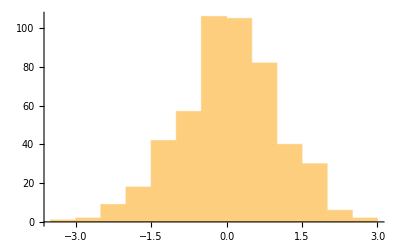
PlotRange[-Graphics-]

```mathematica
PlotRange@Histogram[data1]
```

```mathematica
hhhh//InputForm
```

```mathematica
Options[Insert[hhhh, PlotRange->Automatic, 2], Ticks]
```

{Ticks→{Automatic,Automatic}}

```mathematica
ToSVG@hhhh
```